# MATH299M/CMSC389W - Visualization through Mathematica Week 13: Advanced Dynamic - Proper Use of Dynamic and DynamicModule

In week 10 we provided an introduction to Dynamic, mainly so that you’ve seen it before this week and would recognize it if you saw it in code. Dynamic is a building block of many other tools in Mathematica - this week we will be diving in to learn how to use Dynamic properly. The documentation lies in part in:

Dynamic: https://reference.wolfram.com/language/ref/Dynamic.html
DynamicModule: https://reference.wolfram.com/language/ref/DynamicModule.html
Introduction to Dynamic: https://reference.wolfram.com/language/tutorial/IntroductionToDynamic.html
Control Objects: https://reference.wolfram.com/language/tutorial/IntroductionToControlObjects.html
Control Options: https://reference.wolfram.com/language/guide/ControlsOptions.html
DynamicVisualization: https://reference.wolfram.com/language/guide/DynamicVisualization.html
Advanced Dynamic Functionality: https://reference.wolfram.com/language/tutorial/AdvancedDynamicFunctionality.html

A summary of which is explained here. As usual with Mathematica, the documentation is wonderful, however in this case it is very long. You may find Wolfram’s explanation useful though. I purposefully do not copy code from the documentation to a) keep these documents original and b) give you a diversity of examples should you consult the documentation.

Dynamic

In Lesson 10 we introduced Dynamic, showing its ability to link variables to make them dynamically updated in their output cells. See Lesson 10 for a review on how this works.
The Dynamic function follows through to the Output, but is simply invisible in the front end, meaning that you have to place it around everything that needs to be evaluated, as our functions don’t know what to do with a Dynamic[] object - here’s an example of “do” and “don’t”:

```mathematica
{Slider[Dynamic[a],{-5,5}],Dynamic[Plot[a x,{x,-5,5},PlotRange->5,PlotLabel->"Do"]],Plot[Dynamic[a] x,{x,-5,5},PlotRange->5,PlotLabel->"Don't"]}
```

{,,-Graphics-}

### Second Argument of Dynamic - Update (Inverse) Function

Next we investigate the second argument of Dynamic, which allows you to specify an inverse function that tells a Control Object how it’s supposed to handle the expression in the first argument - the first argument’s expression need not be just a variable, but in the event that it is anything else, Mathematica does not default a way that it should be controlled. Control Objects continuously apply the line expr=new to update the value, so your inverse function will have to include this detail. Notice below that in the first example you cannot move the slider, but in the second example you can, and in the third the inverse function imposes something extra, namely steps.

```mathematica
{Slider[Dynamic[1-y],{0,5}],Dynamic[1-y]}
```

{,}

```mathematica
{Slider[Dynamic[1-y,(y=1-#)&],{0,5}],Dynamic[1-y]}
```

{,}

```mathematica
{Slider[Dynamic[1-y,(y=Floor[1-#])&],{0,5}],Dynamic[1-y]}
```

{,}

Dynamic keeps track of the dependencies of everything inside the brackets and reevaluates if and only if something inside there changes. For this reason we would like to avoid putting too much inside of Dynamic blocks. Here’s an example of passing more into the Dynamic than necessary; we can see that the first version with x2 and y2 in separate Dynamics is smooth because x2 is all that’s being updated, but the second version is slow and choppy because any time you move the x2 slider it re-draws the mess of spheres to the screen.

```mathematica
x2=0.5;
y2=Graphics3D[{Table[{RGBColor[Table[RandomReal[],{k,1,3}]],Sphere[Table[RandomReal[{-5,5}],{k,1,3}],RandomReal[{.001,1}]]},{l,1,500}]}];
Slider[Dynamic[x2]]
TabView[{{Dynamic[x2],Dynamic[y2]},Dynamic[{x2,y2}]}]
```

12

### How Dynamic values are updated

Dynamic values are updated only when necessary. Each computer cycle (by default up to 20 times per second, can be changed by setting DynamicUpdateInterval) any value that is updated is marked and everything depended on it is updated (in summary). Things off-screen are not updated until they are looked at again, so it’s not a good idea to have things depend on dynamic output since it only exists when observed, Schrödinger-style.

### Refresh and TrackedSymbols

Mathematica has a system for efficiently updating everything that needs to be updated dynamically in response to Control Objects and other Dynamic blocks, however sometimes you may wish to control explicitly the dependencies for re-evaluating Dynamic blocks, that is, you may want to remove or add some conditions for when to refresh the value. To do this, take an expression that you are placing inside of a Dynamic block, and around the expression call Refresh with the expression being the first argument, and the second argument of Refresh being the Option TrackedSymbols set to a list of variables for which their update forces the expression to dynamically update.

```mathematica
DynamicModule[{a,b,c,d},Column[{Dynamic[MatrixForm[Refresh[({{a, b}, {c, d}}),TrackedSymbols->{a}]]],Slider[Dynamic[a],{-5,5}],Slider[Dynamic[b],{-5,5}],Slider[Dynamic[c],{-5,5}],Slider[Dynamic[d],{-5,5}]}]]
```

This matrix only updates its values when a is changed, otherwise it doesn’t bother. This feature can be used to do specific code-specific things to get certain behaviour, as well as reduce calculation time behind the scenes when it’s not necessary, as well as to add extra refresh dependencies - although, theoretically, this usage shouldn’t be needed unless you’re restricting away dependencies also, since Mathematica if left to its own devices is thorough about the dependencies.

### SynchronousUpdating

The Kernel and front end are two separate threads, and they communicate through three WTSP (Wolfram Symbolic Transfer Protocol) connections. These connections are the Main Link for Shift+Enter evaluations, the Preemptive Link for Dynamic updates, and the Service Link which goes backwards sending requests from the Kernel to the front end. The SynchronousUpdating Option by default is False; what this means is that the fast Preemptive Link updates from Dynamic blocks is allowed to interrupt the long slow Main Link evaluations, so the calculations appear to happen simultaneously. Turning on the SynchronusUpdating Option makes it so the Preemptive Link requests to the Kernel have to wait for the Main Link’s request to completely finish, they’re “synchronized” (feels like this should mean the other state), freezing up the front end until it’s done.
SynchronusUpdating can be set to Automatic to have nice properties, such as the grey box (see ImageSizeCache in the documentation) while loading to be the right size so there isn’t rescaling once the actual image comes in.

Control Objects

Control Objects are interactive structures that are linked to a value of a variable. That variable can be made a dynamically updated variable but enclosing it in Dynamic[], making the Control Objects useful for altering things in the Output cell object, just like Manipulate’s sliders etc. If the Control Object is linked to a variable that isn’t dynamically updated, then it’s essentially useless, as it is then altering the value of a local copy of a variable that lives in the object in the Output cell but has no scope to reach anything else.
For Control Objects generally you use Dynamic around everything in the first argument.
You’ll notice my variable names get more specific in this section so that we don’t have every control object dynamically linked to the same “x” variable.

### Slider, VerticalSlider, Slider2D and IntervalSlider

Slider takes in one or two arguments. The first is the variable you would like to be linked to the Slider, which can be put inside of a Dynamic[] block to make it a dynamically updated variable, and the second argument is a domain 2-tuple containing a min then a max for the slider or a 3-tuple where the added third element is a step size for the slider.

```mathematica
xSliderExample1=0;
{Slider[xSliderExample1,{0,5}],xSliderExample1}
```

{,0}

```mathematica
xSliderExample1^2
```

Notice here that since the Slider created a new object in the Output cell and xSliderExample1 isn’t dynamically linked to anything, we don’t actually get anything useful out of the Slider, it’s just manipulating a local variable whose scope can’t reach anything else. Let’s use the dynamic functionality:

```mathematica
{Slider[Dynamic[xSliderExample2],{-2,5}],Dynamic[xSliderExample2]}
```

{,}

VerticalSlider works the exact same way

```mathematica
{VerticalSlider[Dynamic[xSliderExample3]],Dynamic[xSliderExample3]}
```

{,}

```mathematica
xy={1,1};
{Slider2D[Dynamic[xy,(xy=#/Norm[#])&],{{-1.2,-1.2},{1.2,1.2}},ImageSize->{150,150}],Dynamic[xy]}
```

{,}

In this example we use the second argument of Dynamic to pin the 2D Slider to the unit circle.

```mathematica
{IntervalSlider[Dynamic[range],{-10,10}],Dynamic[range]}
```

{,}

### Manipulator

Exactly the same as Slider except it adds some controls underneath - look familiar?
You can use the Appearance Option to default it to Open or Closed, or set it to Labeled to get the number printed to the right of the slider.
This has great options, you should check out the documentation: https://reference.wolfram.com/language/ref/Manipulator.html

```mathematica
Manipulator[Dynamic[manip],Appearance->"Open"]
```

### Button

You’ll recognize this from Lesson 3 where we tackled Manipulate Options. Button takes in two arguments, the first is what is to be printed on the Button, which can be text, a graphic, or anything else (as is the standard with Mathematica), and the second argument is what to be implemented, that is, a body of commands. Let’s see a simple example.

```mathematica
OneUpMushroom=Magnify[Import["https://www.mariowiki.com/images/thumb/b/b4/1-Up_Mushroom_Artwork_-_Super_Mario_3D_World.png/1200px-1-Up_Mushroom_Artwork_-_Super_Mario_3D_World.png"],.3];
lives=3;
```

```mathematica
{Button[OneUpMushroom,{lives++}],Dynamic["Lives = "<>ToString[lives],lives]}
```

{-Graphics-,}

### CheckBox and RadioButton

```mathematica
{Checkbox[Dynamic[ballot]],Dynamic[ballot]}
```

{,}

RadioButton takes two arguments, the first is a variable and the second is what to set it to when the RadioButton is pressed.

```mathematica
lightSwitch="Off";
{RadioButton[Dynamic[lightSwitch],"On"],RadioButton[Dynamic[lightSwitch],"Off"],Dynamic[lightSwitch]}
```

{,,}

### InputField

```mathematica
{InputField[Dynamic[custom]],Dynamic[custom]}
```

{,}

### FileNameSetter, PasteButton, ColorSetter

```mathematica
{FileNameSetter[Dynamic[filePath]],Dynamic[filePath]}
```

{$CellContext`filePathOpenAll,}

```mathematica
PasteButton["Pastes expression whever your cursor is","Hello World!"]
```

Pastes expression whever your cursor is

```mathematica
"Hello World!""Hello World!""Hello World!""Hello World!""Hello World!"
```

```mathematica
ColorSetter[Dynamic[col]]
```

$CellContext`col

### TabView

TabView very simply displays an array of different options each associated with its own tab, the tab’s names defaulting to 1, 2, 3, ... but they can be specified by adding -> whatever for each one.

```mathematica
TabView[{"1-Up"->Magnify[OneUpMushroom,.2],"Prototype"->Magnify[Graphics3D[{Green,Sphere[{0,0,0},1]}],.2]}]
```

12

### SlideView, FlipView, MenuView, OpenerView, PopupView

```mathematica
Map[#[{"Apple","Orange","Dragon Fruit","Momochino","Mango"}]&,{SlideView,FlipView,MenuView,PopupView}]
```

{,,,}

```mathematica
OpenerView[{"Pokemon",Column[{"Bulbasaur","Squirtle","Charmander","Pikachu"}]}]
```

### Locator and LocatorPane

Locator, as you know from our week on Manipulate, is a little locator that you can drag around the screen which corresponds dynamically to a value - we now can see rigorously how that works. Locator is a Graphics primitive that just takes one argument, which you can wrap in Dynamic. LocatorPane takes two arguments, the first is a list of points to put Locators on, and the second is a background, which must be a Graphics window or something. Don’t forget in LocatorPane to wrap the list (the first argument) in Dynamic.

```mathematica
locEx={0,0};
{Graphics[Locator[Dynamic[locEx]]],Dynamic[locEx]}
```

{-Graphics-,}

```mathematica
locEx1={0,0};locEx2={.5,0};locEx3={0,.5};
LocatorPane[Dynamic[{locEx1,locEx2,locEx3}],Dynamic[Graphics[Triangle[{locEx1,locEx2,locEx3}],PlotRange->.7]]]
```

Also remember that LocatorAutoCreate is a thing - it’s an Option of LocatorPane as well as Manipulate.

```mathematica
locs={{0,0},{0,.5},{.5,0}};
LocatorPane[Dynamic[locs],Dynamic[Graphics[Polygon[locs],PlotRange->.7]],LocatorAutoCreate->True]
```

### CreatePalette

CreatePalette pops out a little notebook window to do things (see DynamicModule wormholes below for how to get it to interact with the DynamicModule you popped it from). The only argument of CreatePalette is the expression you want to be in the window. It can be a number, a plot or graphic, something dynamic/interactive, or even a whole notebook.

```mathematica
DynamicModule[{},Column[{Button["I Forgot the Controls",{CreatePalette[Column[{Style["a to Jump",FontSize->20,Bold],Style["b to Crouch",FontSize->20,Bold],Style["x to Reload",FontSize->20,Bold],Style["y to Switch",FontSize->20,Bold]}]]}],Button["Tell Me a Joke",{CreatePalette[WolframAlpha["Tell me a joke"]]}]}]]
```

Controls Options

For any Control Object you can set Options for aesthetic purposes, namely ImageSize, ImageMargins, BaselinePosition and ContentPadding which are self-explanatory. You can also use the Appearance Option, which also lets you control size as well as a few presets: “Palette”, “Frameless”, “FramedPalette” and “DialogBox”, which actually reach down and depend on your operating system for appearance - here are some examples:

```mathematica
normalMario=Import["http://mario.nintendo.com/assets/img/characters/char-mario-action.png"];
mushroom=Magnify[Import["https://www.mariowiki.com/images/thumb/9/94/MushroomMarioKart8.png/1206px-MushroomMarioKart8.png"],.33];
megaMushroom=Magnify[Import["https://www.mariowiki.com/images/thumb/e/e0/Mega_Mushroom_-_MTUS.png/1353px-Mega_Mushroom_-_MTUS.png"],.33];
miniMushroom=Magnify[Import["https://www.mariowiki.com/images/5/57/Powerup-mini-mushroom-sm.png"],.33];
superStar=Magnify[Import["https://www.mariowiki.com/images/thumb/6/64/Super_Star_Artwork_-_Super_Mario_3D_World.png/1060px-Super_Star_Artwork_-_Super_Mario_3D_World.png"],.33];
invincibleMario=Magnify[RemoveBackground[Import["https://www.mariowiki.com/images/thumb/8/85/Nsmb2_starman_mario.png/440px-Nsmb2_starman_mario.png"]],1.2];
```

```mathematica
DynamicModule[{size=1,col=White,invincible=False},{Button[mushroom,{size*=1.1},Appearance->"Palette"],Button[megaMushroom,{size*=2},Appearance->"Frameless"],Button[miniMushroom,{size/=3},Appearance->"FramedPalette",Enabled->Dynamic[!invincible]],Button[superStar,invincible=!invincible,Appearance->Dynamic[If[invincible,{"Pressed","DialogBox"},{"DialogBox"}]]],Dynamic[Magnify[Style[If[invincible,invincibleMario,normalMario],Background->col],.25 size]]}]
```

There’s a lot going on here. The buttons each have a different Appearance to showcase those options, the image of Mario is inside of a Magnify function using parameter size which is one of our DynamicModule local variables and changeable with bodies of the Mushroom Buttons, the Super Star Button toggles the Boolean variable invincible which determines which image of Mario to use (the invincbleMario image has its background removed with RemoveBackground) and the Super Star Button has a Dynamic value of Appearance, namely that when invincible is True it has the option Pressed set to showcase that it is on. Furthermore, notice that we encased the Option for Appearance for the Super Star Button in Dynamic because it depends on invincible which is dynamically updated, and Mini Mushroom has the options Enabled set to the negation of invincible (also in a Dynamic block), disabling the Mini Mushroom button when Mario is invincible - this disabling shades it out (subtly) and makes clicks not register. Notice that it is okay to put Dynamic around an Option setting but not okay to put it around something inside Plot’s first two arguments - that’s because Dynamic delays evaluation until it gets to the front end, and while some Options are evaluated in the front end (like PlotRange), the first two arguments need to be evaluated right away for Plot to work. More on this in Lesson 15 (Evaluation Control).

### Method

An option for Control Objects is Method, which defaults to “Preemptive” and can be set to “Queued”. When it is set to Preemptive the Button’s body will use the Preemptive link so it can jump into a large calculation - you could use this to make an abort Button. When set to Queued it uses the Main link, this is good if the Button is going to do something that will take longer.

```mathematica
go=False;methodEx=0;
{Dynamic[methodEx],Button["Start Increasing",{go=True}],Button["Stop",{go=False}],Dynamic[If[go,Dynamic[methodEx=methodEx+1;]]]}
```

{,Start Increasing,Stop,}

Thanks to the Preemptive setting of the Stop Button, we are able to interrupt that last Dynamic Main link and change the value we need to.

### ContinuousAction Option

ControlObjects have the Boolean Option ContinuousAction which can be turned to False to make it so the control will not respond to the user while it actively being interacted with. This can help take out calculations that aren’t going to finish in time anyway. Here’s an example:

```mathematica
Slider[Dynamic[k],{-4,30},ContinuousAction->False]
Dynamic[ContourPlot3D[x^2+y^2+z^2-x y z-2==k,{x,-5,5},{y,-5,5},{z,-5,5},Mesh->None,PlotPoints->18]]
```

### ControlActive

ControlActive is a function to be put nested somewhere in a Dynamic (or anywhere, theoretically), and returns its first argument if some control is Active and returns its second argument if the Control is not Active.

```mathematica
Slider[Dynamic[levelSet],{-4,20}]
Dynamic[ContourPlot3D[x^2+y^2+z^2-x y z-2==levelSet,{x,-5,5},{y,-5,5},{z,-5,5},Mesh->None,PlotRange->5,PlotPoints->ControlActive[5,50]]]
```

ControlActive when being switched from True to False carries out the task of updating all Dynamics associated with what was just being controlled, however it has no behaviour for switching from False to True, that is, if ControlActive isn’t updated for some other reason, it will not update its value to False.

DynamicModule

DynamicModule creates an object in the Output cell that stores values of the chosen variables there instead of in the Kernel. Much like Module, these values are local and so independent from other variables of the same name outside of the DynamicModule. An important difference from Module is that variables are stored in the object embedded in the Output cell, rather than in the Kernel like with Module, so when you quit the Mathematica session DynamicModule will store the values of the Control Objects in the Output cell objects, while Module would lose such information when you quit the Kernel. Furthermore, Module variables technically have a chance at colliding with Modules from other notebooks - Module creates new versions of the variables with different names (of the form, for example, x$654) which can coincidentally be shared by other Modules. DynamicModule avoids this by storing values uniquely when it gets to the Output cell. A way to think of the difference between Module and DynamicModule is that Module rents out variables for a certain amount of time to get a calculation done with the desired scoping, while DynamicModule rents out space for doing things, and this space persists Mathematica sessions. This persistence is called “freeze-drying” the variables, that is, when you close the Mathematica session and then reopen the notebook, the variable values in a DynamicModule have been preserved and are waiting there for you.

Just like Module, the first argument is a list of private variables, which can be initialized if you wish, and the second argument is a list of things to make, that is, your dynamic output and Control Objects.

```mathematica
{Slider[Dynamic[x],{-10,10}],Dynamic[x]}
DynamicModule[{x=0},{Slider[Dynamic[x],{-10,10}],Dynamic[x]}]
```

{,}

### DynamicModule - who owns variables

Normally variable values reside in the kernel, so an interactive session (dynamically updated content) has to consult the kernel every time one of those variables is retrieved or updated. DynamicModule variables, however, reside in the front end in the Output cell meaning they can be retrieved much faster. A draw back is that these variables will take space in file storage since the notebook saves them, but that is often worth the cost. Here’s an example of where having the variable stored in the front end speeds things up dramatically (unmute the Table lines to see what’s going on):

```mathematica
x1=.5;
Slider[Dynamic[x1]]
Table[Dynamic[x1],{k,1,1000}];
```

```mathematica
DynamicModule[{x2=.5},{Slider[Dynamic[x2]],Table[Dynamic[x2],{k,1,1000}]}];
```

We see that the latter is much smoother.

### DynamicModule wormholes

Sometimes within DynamicModule we would like to create another DynamicModule that shares the same variable scope as its parent. A dynamic object in the inner DynamicModule may set the option InheritScope in order to do just this - even if that Object is a separate window.

```mathematica
cookie=Import["https://vignette.wikia.nocookie.net/cookieclicker/images/5/5a/PerfectCookie.png/revision/latest/scale-to-width-down/250?cb=20130827014912"];
DynamicModule[{clicks=0},{Dynamic[ToString[clicks]<>" Cookie"<>If[clicks≠1,"s",""]],Button["Clicker Spawn",{CreatePalette[DynamicModule[{},Button[cookie,clicks++],InheritScope->True]]}]}]
```

Formatting Constructs

Formatting constructs are useful for arranging Control Objects and other outputs how you wish, allowing for arbitrary control over the user interface you would like to construct.

### Grid, Row and Column

Besides Style, the most common and useful of these are Grid, Row and Column, which arrange their argument, a list of lists for Grid and a list for Row and Column, how you would expect given the name, that is, Grid will organize the arbitrary elements into a row - major grid, Row will put the elements (so, in the example below, 2 - tuples) into a row, and column, into a column. Note that these formats are persistent in Output, meaning that if you use these Outputs as Inputs, the Grid, Row or Column wrapper will follow.

```mathematica
testList={{Slider[Dynamic[xFormat]],Button["Hello",{Print["Hello World!"]}]},{TabView[{"Apple","Orange"}],Slider2D[Dynamic[{xTupleFormat,yTupleFormat}]]}};
Grid[testList]
```

| Hello
12 |

```mathematica
Row[testList]
```

{,Hello}{12,}

```mathematica
Column[testList]
```

{,Hello}
{12,}

Hello World!

We can of course nest these however we wish, and we can utilize helpful display Options like Alignment. Furthermore, the optional second argument of Row and Column is a Spacer, that is, what to put between each element, which in this case we would like to be some empty space.

```mathematica
Column[{Style["Pascal's Triangle",Bold],Row[{1}],Row[{1,1},"  "],Row[{1,2,1},"  "],Row[{1,3,3,1},"  "],Row[{1,4,6,4,1},"  "],Row[{1,5,10,10,5,1},"  "],Row[{".",".",".",".","."},"   "]},Alignment->Center]
```

Pascal's Triangle
1
    11
    121
    1331
    14641
    15101051
      .....

### Panel

Panel takes one argument, an expression, and simply places that expression into a grey box, a Panel. It has Options Background, Enabled, FrameMargins, Alignment, etc.

```mathematica
Row[{Deploy[Panel[Panel[Slider[Dynamic[panelEx]]]]],"   ",Deploy[Column[{Panel[Slider[Dynamic[panelEx2]]],Panel[Slider[Dynamic[panelEx]]],Panel[Slider[]]},Alignment->Center]]}]
```

### Deploy

Deploy outputs the expression it takes as its one argument and disables all interactivity besides that of the Control Objects, so we can’t select the box and stuff.

```mathematica
xy2={0,0};
{Dynamic[Graphics[Point[xy2],PlotRange->2]],Slider2D[Dynamic[xy2],{{-1,-1},{1,1}}]}
Deploy[{Dynamic[Graphics[Point[xy2],PlotRange->2]],Slider2D[Dynamic[xy2],{{-1,-1},{1,1}}]}]
```

{,}

```mathematica
{,}
```

Notice that you can’t select the Graphics pane in the second line (the Deploy-d one). This makes a more seamless user interface.

### Labeled

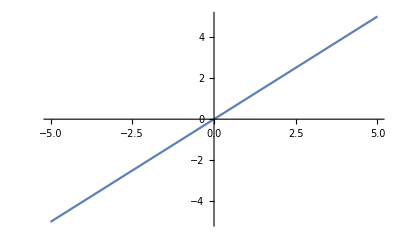
This is a mighty fine Plot-Graphics-

```mathematica
Labeled["This is a mighty fine Plot",Plot[x,{x,-5,5}]]
```

Auto-play - making a ticker

You can create a sort of game clock by defining a dynamic element that constantly updates itself, this will go on forever.
WARNING: READ THIS BEFORE PLAYING WITH THE THING BELOW
Okay, go ahead and run the cell below BUT DON’T CHANGE ANYTHING. If you’re anything like me, you’re itching to make that increase more dramatic - go ahead, change it to x *= 2. Cool huh? Mathematica doesn’t seem to have an overflow for huge numbers. Okay, now before you change it to x = x^2 or x = x! or x = x^x, fair warning that it will keep going an eating up more RAM and freeze the window, forcing you to force quit Mathematica - then when you open the notebook again you have to turn off “Dynamic Updating Enabled”, quit the Kernel, delete the output cell, and still cross your fingers - I ended up restarting my computer and then had to Ctrl-A Ctrl-C all of the contents of this notebook into a new notebook b/c for some reason this one crashed every time you try to use^(the carrot) which is why I’ve called it the Carrot^Crash and it’s cause is currently unknown. Anyway, you’ve been warned.

```mathematica
DynamicModule[{x=1},Dynamic[x=x+1]]
```

An implementation of this idea that doesn’t crash your session, a so-called “Droopy Slider”:

```mathematica
x=1;
{Slider[Dynamic[x]],Dynamic[x=Max[0,x-.0015]]}
```

Now keeping things like that running makes me nervous - so I’ve deleted the Output cell above, you probably should too when you’re done.
These things aren’t crash-machines, they’re supposed to cooperate with your code just fine. This notebook specifically might be an issue since there’s so much dynamically updated stuff going on.
Also good to note is that due to Mathematica’s dynamic tracking system, when this droopy slider hits 0 the load on your CPU will be lifted (you can see this in Activity Monitor on your device or with MemoryInUse[]) as it has detected that nothing is changing anymore.

EventHandler

We would now like to integrate the feature for the model to respond to key presses. The idea is that while your dynamically-updated model is running if you click on it and then press a specified key, an arbitrary action will happen, such as updating certain variables. EventHandler should be placed inside the second argument of a DynamicModule, its first argument is a body, so the entirety of what you would have had been the second argument of the DynamicModule, followed by a list of associations of key presses to bodies that tell the model what to do in those cases. The key presses are formatted as, for example, {“KeyDown”,”x”} or “UpArrowKeyDown”. Here’s an example:

```mathematica
DynamicModule[{x={0,0}},EventHandler[Graphics[{PointSize[.1],Dynamic[Point[x]]},PlotRange->5],{"UpArrowKeyDown":>(x+={0,.1}),"DownArrowKeyDown":>(x-={0,.1}),{"KeyDown","r"}:>(x=0)}]]
```

Note: I have been able to get EventHandler to respond to UpArrowKeyDown, DownArrowKeyDown, etc. and {“KeyDown”,”1”} and the other numbers together, but for some reason when a letter is introduced it can only handle one at a time, that is, the second letter control is always ignored - I need to iron this out.

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 December 2nd, 2018